## Nomenclature

1=F=1,m_F=0,0ℏk
2=F=2,m_F=0,0ℏk
3=F=1,m_F=0,2ℏk

Spin operators (J_(x,y,z))^ij is defined as the operator J_(x,y,z) between state i and j

### Operator for 12 (microwave rotation)

RotEq mean a rotation along ax axis ϕ on the equator by θ
ϕ=0 means rotate along x-axis, ϕ=π/2 means rotate along y-axis

```mathematica
Sx12=({{0, 1, 0}, {1, 0, 0}, {0, 0, 1}})/2; Sy12=({{0, -ⅈ, 0}, {ⅈ, 0, 0}, {0, 0, 1}})/2; Sz12=({{1, 0, 0}, {0, -1, 0}, {0, 0, 1}})/2;
RotEq12[ϕ_,θ_]:=MatrixExp[-ⅈ θ (Cos[ϕ] Sx12+Sin[ϕ]Sy12)]
Rotz12[θ_]:=MatrixExp[-ⅈ θ Sz12]
```

### Operator for 23 (Raman rotation)

```mathematica
Sx23=({{1, 0, 0}, {0, 0, 1}, {0, 1, 0}})/2; Sy23=({{1, 0, 0}, {0, 0, -ⅈ}, {0, ⅈ, 0}})/2; Sz23=({{1, 0, 0}, {0, 1, 0}, {0, 0, -1}})/2;
RotEq23[ϕ_,θ_]:=MatrixExp[-ⅈ θ (Cos[ϕ] Sx23+Sin[ϕ]Sy23)]
Rotz23[θ_]:=MatrixExp[-ⅈ θ Sz23]
```

### Operator for 13 (Bragg rotation)

```mathematica
Sx13=({{0, 0, 1}, {0, 1, 0}, {1, 0, 0}})/2; Sy13=({{0, 0, -ⅈ}, {0, 1, 0}, {ⅈ, 0, 0}})/2; Sz13=({{1, 0, 0}, {0, 1, 0}, {0, 0, -1}})/2;
RotEq13[ϕ_,θ_]:=MatrixExp[-ⅈ θ (Cos[ϕ] Sx13+Sin[ϕ]Sy13)]
Rotz13[θ_]:=MatrixExp[-ⅈ θ Sz13]
```

### Microwave Ramsey interference

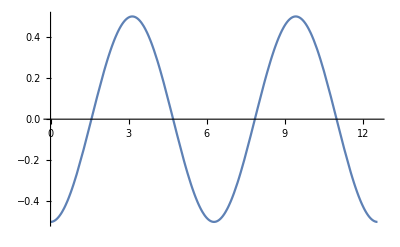

```mathematica
ψini=({{1}, {0}, {0}});
ψf=RotEq12[ϕ,π/2].RotEq12[0,π/2].ψini;
Plot[Transpose[Conjugate[ψf]].Sz12.ψf,{ϕ,0,4π}]
```

```mathematica
RotEq12[0,π/2]
```

{{1/(√2),-ⅈ/(√2),0},{-ⅈ/(√2),1/(√2),0},{0,0,ⅇ^(-(ⅈ π)/4)}}

This is wired for me. The third component carries a phase...

```mathematica
RotEq12[0,π/2].ψini
```

{{1/(√2)},{-ⅈ/(√2)},{0}}

```mathematica
v=RotEq13[0,π/2].RotEq13[0,π].{{1/(√2)},{-ⅈ/2},{-1/2}}
```

{{-1/2+ⅈ/(2 √2)},{-1/2 ⅇ^(-(ⅈ π)/4)},{-ⅈ/2+1/(2 √2)}}

```mathematica
Abs[v[[3]]]^2
```

{1/8}

```mathematica
RotEq13[0,π].RotEq23[0,Pi].RotEq12[0,π/2].ψini
```

{{ⅈ/(√2)},{0},{-1/(√2)}}

```mathematica
RotEq23[0,α].RotEq12[0,π/2].ψini
```

{{ⅇ^(-(ⅈ α)/2)/(√2)},{-(ⅈ Cos[α/2])/(√2)},{-Sin[α/2]/(√2)}}

```mathematica
RotEq13[0,π+γ].RotEq23[0,π].RotEq12[0,π/2].ψini
```

{{(ⅈ Cos[γ/2])/(√2)+(ⅈ Sin[γ/2])/(√2)},{0},{-Cos[γ/2]/(√2)+Sin[γ/2]/(√2)}}

```mathematica
RotEq13[0,π].RotEq23[0,π/5].RotEq12[0,π/2].ψini
```

{{-(-1/2 (-1)^(1/10)-1/2 (-1)^(9/10))/(√2)},{-(1/2 (-1)^(1/10)-1/2 (-1)^(9/10))/(√2)},{-(ⅈ ⅇ^(-(ⅈ π)/10))/(√2)}}

```mathematica
RotEq13[ϕ,π/2].RotEq13[0,π].RotEq23[0,π/2].RotEq12[0,π/2].ψini
```

{{ⅈ/(2 √2)+1/2 ⅇ^(-(ⅈ π)/4) (-Cos[ϕ]+ⅈ Sin[ϕ])},{-1/2 ⅇ^(-1/4 ⅈ π (Cos[ϕ]+Sin[ϕ]))},{-1/2 ⅈ ⅇ^(-(ⅈ π)/4)-(-Cos[ϕ]-ⅈ Sin[ϕ])/(2 √2)}}

```mathematica
RotEq13[ϕ,π/2].RotEq13[0,π].RotEq23[0,π].RotEq12[0,π/2].ψini
```

{{ⅈ/2-1/2 ⅈ (-Cos[ϕ]+ⅈ Sin[ϕ])},{0},{-1/2+1/2 (Cos[ϕ]+ⅈ Sin[ϕ])}}

```mathematica
RotEq13[ϕ,π/2]//MatrixForm
```

(1/(√2) | 0 | (ⅈ (-Cos[ϕ]+ⅈ Sin[ϕ]))/(√2)
0 | ⅇ^(-1/4 ⅈ π (Cos[ϕ]+Sin[ϕ])) | 0
(ⅈ (-Cos[ϕ]-ⅈ Sin[ϕ]))/(√2) | 0 | 1/(√2))

```mathematica
RotEq13[0,α]//MatrixForm
```

(Cos[α/2] | 0 | -ⅈ Sin[α/2]
0 | ⅇ^(-(ⅈ α)/2) | 0
-ⅈ Sin[α/2] | 0 | Cos[α/2])

### Hybrid interferometer

pi/2|_uwave→ pi|_Raman→ Tevol→ pi|_Bragg→ Tevol→ pi/2|_Bragg

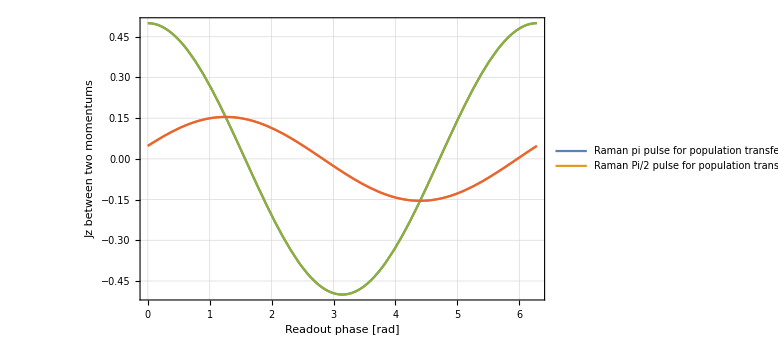

```mathematica
ψini=({{1}, {0}, {0}});
ψf=RotEq13[ϕ,π/2].RotEq13[0,π].RotEq23[0,π].RotEq12[0,π/2].ψini;
ψf1=RotEq13[ϕ,π/2].RotEq13[0,π].RotEq23[0,π/5].RotEq12[0,π/2].ψini;

BM1=Cos[ϕ];
BM2=Sin[π/10]Cos[ϕ-π/2+π/10];

Plot[
{Transpose[Conjugate[ψf]].Sz13.ψf,Transpose[Conjugate[ψf1]].tSz.ψf1,BM1/2,BM2/2},
{ϕ,0,2π},
ImageSize->Large,
PlotLegends->{"Raman pi pulse for population transfer","Raman Pi/2 pulse for population transfer"},
Frame->True,
FrameLabel->{"Readout phase [rad]","Jz between two momentums"},
GridLines->Automatic,
LabelStyle->15]
```